```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy485-optics

## Rough junk

```mathematica
Clear[i, j]
i = Integrate[ Cos[ τ ω]/(σ^2 + (ω - c)^2), {ω, 0, Infinity}]
j = FullSimplify[ %, σ > 0 && c > 0 && τ > 0]
j /.{ c -> Subscript[ω, 0]}

(*i = Integrate[ Cos[ a ω]/(b^2 + (ω - c)^2), {ω, 0, Infinity}]
j = FullSimplify[ %, a > 0 && b > 0 && c> 0]
j /.{ a -> τ, b -> σ, c -> Subscript[ω, 0]}*)
```

ConditionalExpression[-1/(4 σ)ⅈ (2 Cos[(c-ⅈ σ) Abs[τ]] CosIntegral[-(c-ⅈ σ) Abs[τ]]-2 Cos[(c+ⅈ σ) Abs[τ]] CosIntegral[-(c+ⅈ σ) Abs[τ]]+π Sin[(c-ⅈ σ) Abs[τ]]-π Sin[(c+ⅈ σ) Abs[τ]]+2 Sin[(c-ⅈ σ) Abs[τ]] SinIntegral[(c-ⅈ σ) Abs[τ]]-2 Sin[(c+ⅈ σ) Abs[τ]] SinIntegral[(c+ⅈ σ) Abs[τ]]),τ∈Reals&&(Im[c]≠Re[σ]||Im[σ]+Re[c]<0)&&(Im[c]+Re[σ]≠0||Im[σ]>Re[c])]

1/(4 σ)ⅈ (2 Cos[(c+ⅈ σ) τ] CosIntegral[-(c+ⅈ σ) τ]-2 Cos[(c-ⅈ σ) τ] CosIntegral[-c τ+ⅈ σ τ]-Sin[(c-ⅈ σ) τ] (π+2 SinIntegral[(c-ⅈ σ) τ])+Sin[(c+ⅈ σ) τ] (π+2 SinIntegral[(c+ⅈ σ) τ]))

1/(4 σ)ⅈ (2 Cos[τ (ⅈ σ+ω_0)] CosIntegral[-τ (ⅈ σ+ω_0)]-2 Cos[τ (-ⅈ σ+ω_0)] CosIntegral[ⅈ σ τ-τ ω_0]-Sin[τ (-ⅈ σ+ω_0)] (π+2 SinIntegral[τ (-ⅈ σ+ω_0)])+Sin[τ (ⅈ σ+ω_0)] (π+2 SinIntegral[τ (ⅈ σ+ω_0)]))

```mathematica
Clear[i]
i = InverseFourierTransform[sigma^2/(sigma^2 + (Sqrt[omega^2] - a)^2), omega, t]
FullSimplify[i, sigma > 0 && a > 0] // TraditionalForm
```

-1/(2 √(2 π))ⅈ sigma (2 Cos[(a-ⅈ sigma) Abs[t]] CosIntegral[-(a-ⅈ sigma) Abs[t]]-2 Cos[(a+ⅈ sigma) Abs[t]] CosIntegral[-(a+ⅈ sigma) Abs[t]]+π Sin[(a-ⅈ sigma) Abs[t]]-π Sin[(a+ⅈ sigma) Abs[t]]+2 Sin[(a-ⅈ sigma) Abs[t]] SinIntegral[(a-ⅈ sigma) Abs[t]]-2 Sin[(a+ⅈ sigma) Abs[t]] SinIntegral[(a+ⅈ sigma) Abs[t]])

-1/(2 √(2 π))ⅈ sigma (2 -(a-ⅈ sigma) Abs[t] cos((a-ⅈ sigma) Abs[t])-2 -(a+ⅈ sigma) Abs[t] cos((a+ⅈ sigma) Abs[t])+(π+2 (a-ⅈ sigma) Abs[t]) sin((a-ⅈ sigma) Abs[t])-(π+2 (a+ⅈ sigma) Abs[t]) sin((a+ⅈ sigma) Abs[t]))

```mathematica
Clear[i]
i = InverseFourierTransform[sigma^2/(sigma^2 + (omega - a)^2), omega, t]
FullSimplify[i, sigma > 0 && a > 0] // TraditionalForm
```

1/2 ⅇ^(-(ⅈ a+sigma) t) √(π/2) sigma (Sign[t] (1-ⅇ^(2 sigma t)-Sign[Abs[Im[a]-Re[sigma]]]+ⅇ^(2 sigma t) Sign[Abs[Im[a]+Re[sigma]]])+2 (HeavisideTheta[t Sign[-Im[a]+Re[sigma]]] Sign[-Im[a]+Re[sigma]]+ⅇ^(2 sigma t) HeavisideTheta[-t Sign[Im[a]+Re[sigma]]] Sign[Im[a]+Re[sigma]]))

√(π/2) sigma ⅇ^(t (-(sigma+ⅈ a))) (-t ⅇ^(2 sigma t)+t)

```mathematica
Clear[i1, i2]
i1[omega_] = 1/(1 + (omega - 2)^2) + 1/(1 + (omega + 2)^2)
i2[omega_] = 1/(1 + (Abs[omega] - 2)^2)
(* With Abs, this is equivalent to the following: *)
(*i2[omega_] = HeavisideTheta[omega]/(1 + (omega - 2)^2) + HeavisideTheta[-omega]/(1 + (omega + 2)^2)
*)
Plot[{i1[x], i2[x]}, {x, -5, 5}]

Clear[ee]
ee = Integrate[ E^(I omega t)/(a - I omega), {omega, 0, Infinity}]
FullSimplify[ee, t > 0 && a > 0]
```

```mathematica
Simplify[Cos[x + a] + Cos[x - a]]
```

2 Cos[a] Cos[x]

## Problem 1a) Plot:

```mathematica
Manipulate[
Module[{i, j, k},
i[t_] = sigma E^(-sigma Abs[t]) Cos[ omegabar t] Cos[delta t /2] ;
j[t_] = sigma E^(-sigma Abs[t]) Cos[ omegabar t] ;
k[t_] = sigma E^(-sigma Abs[t]) ;
Show[{
Plot[
{
i[t], -i[t],
j[t], -j[t],
k[t], -k[t]
}
,{t, 0, r}
, PlotRange -> Full
, Axes -> True
, PlotRange -> {{0, r}, {-2 sigma, 2 sigma}}
, AxesLabel -> {t, "I" }
, Ticks -> {Table[m Pi /(2 omegabar), {m, 1, 7}]}
]
,
Graphics[{{
Dashed, 
Line[{{0, (sigma/E)},{1/sigma, (sigma/E)}}],
Line[{{1/sigma, (sigma/E)}, {1/sigma, -sigma/E}}]
}
(*,
Text[1/E, {- 0.8, (1/E)}],
Text[1/Γ, {(1/gamma), -0.2}],
Text[E^(-Γ t), {1.4 + 0.2, damped[1.4] + 0.2}]
*)
}
]
}
]
]
,
{{sigma, 2}, 0.1, 10},
{{omegabar, 10}, 10, 50},
{{delta, 87}, 10, 500},
{{r, 1}, 0.1, 40}
]
```

1/(1+(omega-omega0)^2)+1/(1+(omega+omega0)^2)

1/(1+(-omega0+Abs[omega])^2)

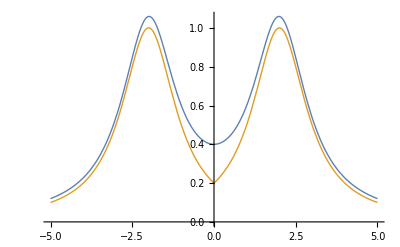

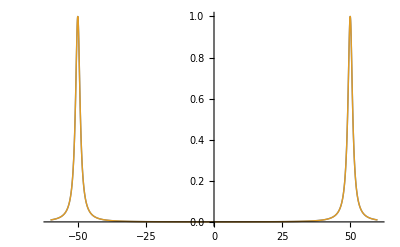

```mathematica
Clear[i1,i2]
i1[omega_, omega0_]=1/(1+(omega-omega0)^2)+1/(1+(omega+omega0)^2)
i2[omega_, omega0_]=1/(1+(Abs[omega]-omega0)^2)
(*With Abs,this is equivalent to the following:*)
(*i2[omega_]=HeavisideTheta[omega]/(1+(omega-2)^2)+HeavisideTheta[-omega]/(1+(omega+2)^2)*)
frequencySingletsFig2 = Plot[{i1[x, 2],i2[x, 2]},{x,-5,5}, PlotStyle->Thick]
frequencySingletsFig3 = Plot[{i1[x, 50],i2[x, 50]},{x,-60,60}, PlotRange -> Full, PlotStyle->Thick]
```

### Part (b)

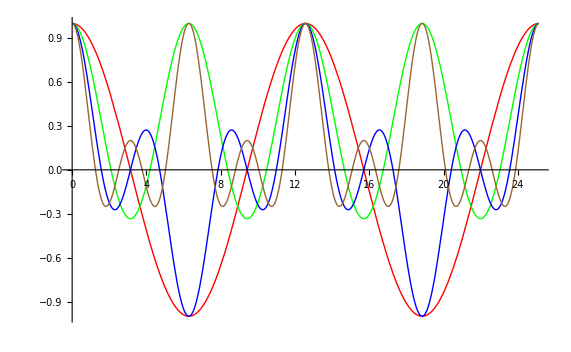

```mathematica
Needs["PlotLegends`"]

Plot[
Tooltip[
{
Sin[2 x/2]/(2 Sin[x/2]),
Sin[3 x/2]/(3 Sin[x/2]),
Sin[4 x/2]/(4 Sin[x/2]),
Sin[5 x/2]/(5 Sin[x/2])
}
]
, {x, 0, 8 Pi}
, Ticks -> {Table[ n Pi, {n, 0, 8}] }
, PlotRange -> Full
,PlotStyle->(Directive[Thick,#]&/@{Red,Green,Blue, Brown})
(*,PlotLegend->{ 1, 2, 3, 4, 5},LegendPosition->{0.95,0.05}*)
(*, ToolTip*)
]
```

```mathematica
Manipulate[
Plot[
Sin[n delta x/2]/(n Sin[x delta/2])
, {x, 0, 8 Pi}
, Ticks -> {Table[ n Pi, {n, 0, 8}] }
, PlotRange -> Full
]
, {{n, 2}, 2, 10, 1}
, {{delta, 1}, 0.1, 10}
]
```

### Final plot for 2(b)

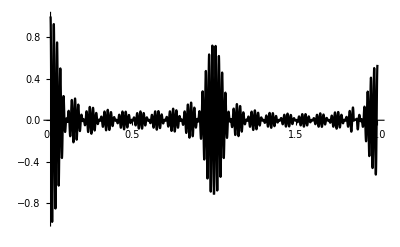

```mathematica
problemSet3Problem1bPlotFig4 = Module[
{sigma,  deltaByTwo, omegabar, n},
sigma = Pi / 10 ;
deltaByTwo = 10 sigma ;
omegabar = 100 deltaByTwo ;
n = 10 ;
(*Show[*)
Plot[
E^(-sigma Abs[u] ) Cos[ omegabar u ] Sin[ n deltaByTwo u ]/(n Sin[ deltaByTwo u])
,{u, 0, 2}
, PlotRange -> Full
, PlotStyle->{(*Thick,*) Black}
, Ticks -> None
(*, AxesLabel -> {u}*)
(*]*)
(*,
Graphics[ 
Text[ E^(-sigma Abs[u] ) Cos[ omegabar u ] Sin[ n deltaByTwo u ]/(n Sin[ deltaByTwo u]), {0.7, 0.9}]
]*)
]
]
```

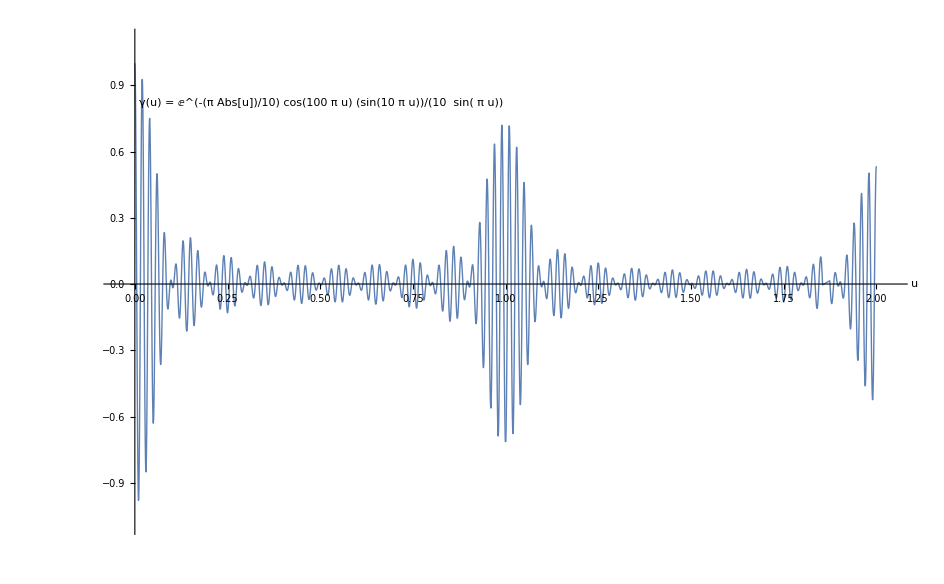
```mathematica
= -Graphics-
```

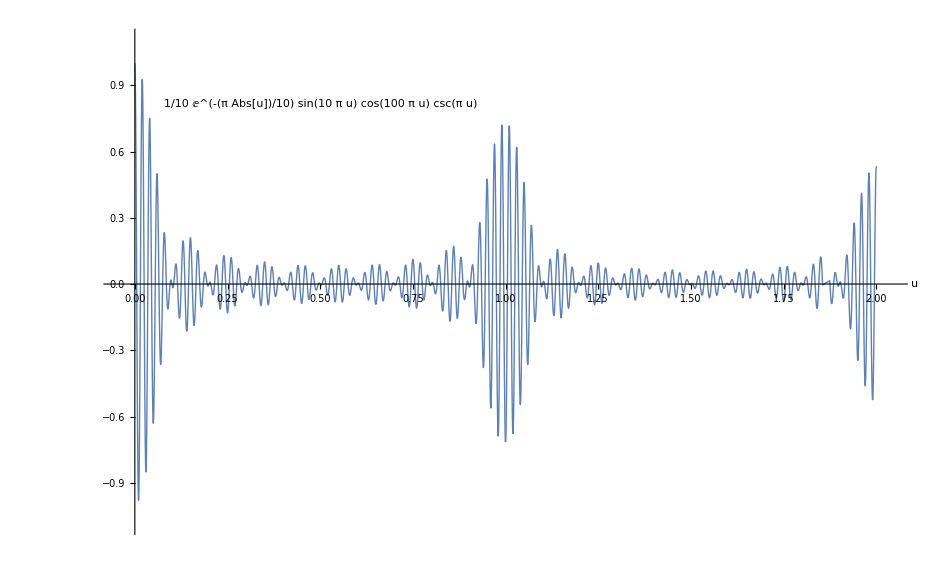

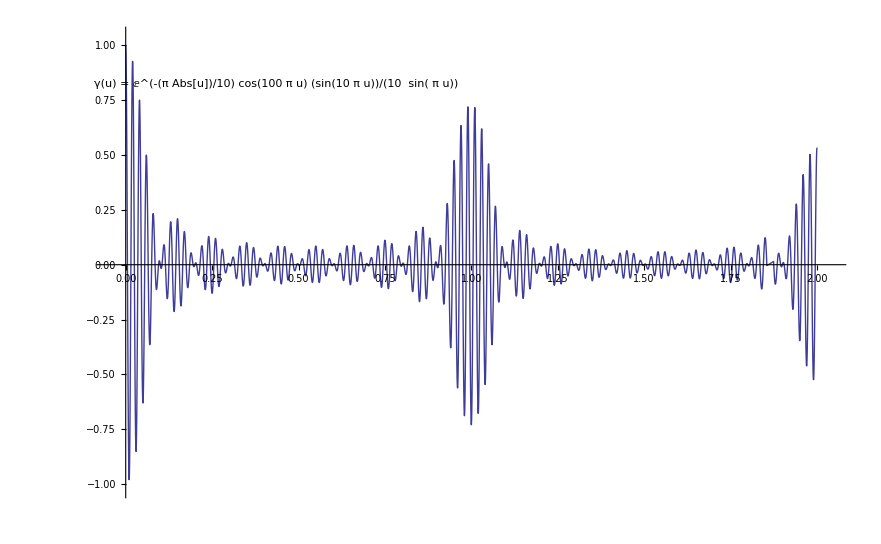

## Problem 3.

### Plot for (a)

(a π Sin[theta])/lambda

(Csc[(a π Sin[theta])/lambda] Sin[(a n π Sin[theta])/lambda])/n

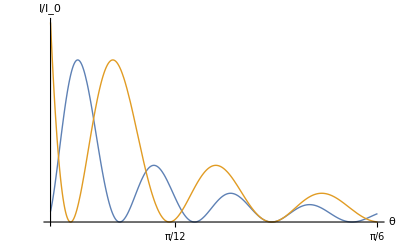

```mathematica
Clear[gamma, n, f]
gamma[lambda_, a_, theta_] = Pi a Sin[theta]/lambda

f[ lambda_, a_, theta_, n_ ] = Sin[ n gamma[ lambda, a, theta ] ]/(n Sin[ gamma[ lambda, a, theta ]])

fs = Style[#, FontSize->14]&;

modernOpticsProblemSet3Problem3Fig3 = Plot[ 
{(f[ 3 Pi 1, 1, theta, 100])^2,
(f[ 4 Pi 1, 1, theta, 100])^2}
, {theta, 0.1, Pi/6}
, Ticks -> {{Pi/12, Pi/6}}
, PlotRange -> Full
, PlotStyle-> Thick
, AxesLabel -> {θ // fs, "I/I_0" //fs}
]
```

```mathematica
(* check equality, verifying hand calculation. *)
Clear[f]
f[x_] = ArcSin[x] ;
f'[x]
f'[x] - 1/Cos[ArcSin[x]]
```

1/(√(1-x^2))

0

### part (c) rough work.

```mathematica
TrigReduce[Cos[ a (m -1/2) ] Cos [ a (n-1/2)]]
Simplify[a (-1/2+m)-a (-1/2+n)]
Simplify[a (-1/2+m)+a (-1/2+n)]
Simplify[(1/2) (Cos[a (-1+m+n)] + Cos[a (m-n)]) - Cos[ a (m -1/2) ] Cos [ a (n-1/2)]]
TraditionalForm[ (1/2) (Cos[a (-1+m+n)] + Cos[a (m-n)])]
Factor[Simplify[(m-1/2)^2 - (n-1/2)^2]]
TrigExpand[1 + Cos[2 x]]
```

1/2 (Cos[a (-1/2+m)-a (-1/2+n)]+Cos[a (-1/2+m)+a (-1/2+n)])

a (m-n)

a (-1+m+n)

0

1/2 (cos(a (m-n))+cos(a (m+n-1)))

(m-n) (-1+m+n)

1+Cos[x]^2-Sin[x]^2

## Problem 2

Part (b)

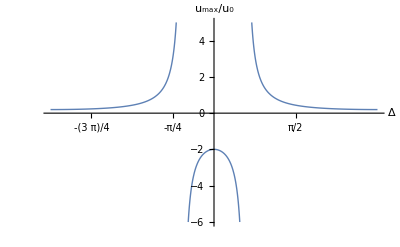

```mathematica
Clear[u]
u[delta_, r_] = (1 -r )(1 + Sqrt[r])^2/(1 + r^2 - 2 Cos[delta]) ;
modernOpticsProblemSet3Problem2Fig2 = Plot[
u[delta, 0.8]
, {delta, -Pi, Pi}
, Ticks -> {{ -Pi/4, -Pi/2, -3 Pi/4, Pi/4, Pi/2, 3 Pi/4 },None}
, AxesLabel -> { Δ // fs , Subscript[u, max]/Subscript[u, 0] // fs}
, PlotStyle->Thick
, PlotRange -> {{-Pi, Pi}, {-6, 5}}
]
```

```mathematica
peeters`exportForLatex["frequencySingletsFig2",frequencySingletsFig2]
peeters`exportForLatex["frequencySingletsFig3",frequencySingletsFig3]
```

{frequencySingletsFig2.eps,frequencySingletsFig2pn.png}

{frequencySingletsFig3.eps,frequencySingletsFig3pn.png}

```mathematica
(*problemSet3Problem1bPlotFig4=*)-Graphics-;
```

```mathematica
peeters`exportForLatex["problemSet3Problem1bPlotFig4",problemSet3Problem1bPlotFig4]
```

{problemSet3Problem1bPlotFig4.eps,problemSet3Problem1bPlotFig4pn.png}

```mathematica
peeters`exportForLatex["modernOpticsProblemSet3Problem3Fig3",modernOpticsProblemSet3Problem3Fig3]
```

{modernOpticsProblemSet3Problem3Fig3.eps,modernOpticsProblemSet3Problem3Fig3pn.png}

```mathematica
peeters`exportForLatex["modernOpticsProblemSet3Problem2Fig2",modernOpticsProblemSet3Problem2Fig2]
```

{modernOpticsProblemSet3Problem2Fig2.eps,modernOpticsProblemSet3Problem2Fig2pn.png}